```mathematica
forkrate[delta_,n_,L_,f_]:=1-n∫_0^∞ (∫_0^∞ (λ p[λ,n,L,f])/ⅇ^(x λ)ⅆλ)(∫_0^∞ p[λ,n,L,f]/ⅇ^((delta+x) λ)ⅆλ)^(n-1) ⅆx
```

```mathematica
p[λ_,n_,L_,f_]:=(∑_(i=1)^n (√(f/(2 π   λ)))/(ⅇ^((Subscript[b, i]-f λ)^2/(2 f λ))))/n
```

```mathematica
B[n_]:=Total[Array[Subscript[b,#]&,n]]
```

```mathematica
MapThread[(Subscript[b,#1]=#2)&,{Range[12],{4,1,3,1,2,3,4,5,7,8,4,5}}]
```

{4,1,3,1,2,3,4,5,7,8,4,5}

```mathematica
FullSimplify[p[λ,2,L]]
```

(ⅇ^(-(L (b_1-(λ (b_1+b_2))/L)^2)/(2 λ (b_1+b_2)))+ⅇ^(-(L (b_2-(λ (b_1+b_2))/L)^2)/(2 λ (b_1+b_2))))/(2 √(2 π) √((L λ)/(b_1+b_2)))

```mathematica
∫_0^∞ (√(λ f / (2 π)))/(ⅇ^(x λ +(Subscript[b, i]-f λ)^2/(2 f λ)))ⅆλ
```

ConditionalExpression[(ⅇ^((2 b_i (f-√(f+x) √(f/b_i^2) b_i))/f) (f+(2 f √(f+x))/(√(f/b_i^2))))/(2 √2 √f (f+x)^(3/2)), Re[f+x]>0&&Re[b_i^2/f]>0]

```mathematica
FullSimplify[(∫_ll^∞ (√(f/(2 π   λ)))/(ⅇ^((Subscript[b, i]-f λ)^2/(2 f λ)))ⅆλ)/n,Subscript[b, i]>0&&f>0&&ll>0]
```

(Erfc[(f ll-b_i)/(√2 √(f ll))]+ⅇ^(2 b_i) Erfc[(f ll+b_i)/(√2 √(f ll))])/(2 n)

```mathematica
FullSimplify[(-1+Erf[(-13 f+Subscript[b, i])/(√26 √f)]+ⅇ^(2 Subscript[b, i]) (-Erf[(13 f+Subscript[b, i])/(√26 √f)]+Erf[(41 f+Subscript[b, i])/(√82 √f)])+Erfc[(-41 f+Subscript[b, i])/(√82 √f)])/(2 n),Subscript[b, i]>0&&f>0]
```

```mathematica
Limit[(-1+Erf[(-√(p f)+Subscript[b, i])/(√(2 p f))]+ⅇ^(2 Subscript[b, i]) (-Erf[(p f+Subscript[b, i])/(√(2 p f))]+Erf[(q f+Subscript[b, i])/(√(2 q f))])+Erfc[(-q f+Subscript[b, i])/(√(2 q f))])/(2 n),q->∞]
```

ConditionalExpression[(1+Erf[(-f p+b_i)/(√2 √(f p))]+ⅇ^(2 b_i) (1-Erf[(f p+b_i)/(√2 √(f p))]))/(2 n), ]

```mathematica
Limit[(1+Erf[(-f p+Subscript[b, i])/(√2 √(f p))]+ⅇ^(2 Subscript[b, i]) (1-Erf[(f p+Subscript[b, i])/(√2 √(f p))]))/(2 n),p->0]
```

$Aborted

```mathematica
aa[a,∞]
```

```mathematica
(-1+Erf[(-a f+Subscript[b, i])/(√2 √(a f))]+ⅇ^(2 Subscript[b, i]) (-Erf[(a f+Subscript[b, i])/(√2 √(a f))]+Erf[(f ∞+Subscript[b, i])/(√(f ∞))])+Erfc[(f (-∞)+Subscript[b, i])/(√(f ∞))])/(2 n)
```

(-1+Erf[(-a f+b_i)/(√2 √(a f))]+ⅇ^(2 b_i) (-Erf[(a f+b_i)/(√2 √(a f))]+Erf[(f ∞+b_i)/(√(f ∞))])+Erfc[(f (-∞)+b_i)/(√(f ∞))])/(2 n)

```mathematica
∫_13^l (√(f/(2 π   λ)))/(ⅇ^((Subscript[b, i]-f λ)^2/(2 f λ)))ⅆλ
```

```mathematica
∫_ll^∞ (ⅇ^(-(-f λ+Subscript[b, i])^2/(2 f λ)) √(f/λ))/(√(2 π))ⅆλ
```

$Aborted

```mathematica
FullSimplify[(∑_(i=1)^n ∫_0^∞ (λ ((√(f/(2 π   λ)))/(ⅇ^((Subscript[b, i]-f λ)^2/(2 f λ))))/n)/ⅇ^(x λ)ⅆλ)(∑_(i=1)^n ∫_0^∞ (((√(f/(2 π   λ)))/(ⅇ^((Subscript[b, i]-f λ)^2/(2 f λ))))/n)/ⅇ^((delta+x) λ)ⅆλ)^(n-1),f>0&&x>0]
```

(∑_(i=1)^n ConditionalExpression[(ⅇ^(-(√(2 delta+f+2 x))/(√f √(1/b_i^2))+b_i) √f)/(n √(2 delta+f+2 x)), f+2 x+2 Re[delta]>0&&Re[b_i^2]/f>0])^(-1+n) ∑_(i=1)^n ConditionalExpression[(ⅇ^(-(√((f+2 x)/f))/(√(1/b_i^2))+b_i) (f+(√(f (f+2 x)))/(√(1/b_i^2))))/(√f n (f+2 x)^(3/2)), Re[b_i^2]/f>0]

```mathematica
forkrate2[delta_,n_,L_,f_]:=1-∫_0^∞ ((∑_(i=1)^n ⅇ^(Subscript[b, i](1-√(1+(2 x)/f))) (1+Subscript[b, i] √(1+(2 x)/f)))/(f ( 1+(2 x)/f)^(3/2)))((∑_(i=1)^n ⅇ^(Subscript[b, i](1-√(1+(2(delta+x))/f))))/(n √(1+(2(delta+x))/f)))^(n-1) ⅆx
```

```mathematica
∫_0^∞ p[λ,3,0.4]ⅆλ
```

```mathematica
N[forkrate[2,2,0.3,B[2]/0.3]]
```

0.254307

```mathematica
1-2 N[ ∫_0^∞ 1/(√(3.289202157232504+0.3183098861837907 x) (8.333333333333334+1. x)^(3/2))54.598150033144236 (44.46132208574461 ⅇ^(-1.3856406460551018 √(10.333333333333334+1. x))+2.2135988824085864 ⅇ^(-0.34641016151377557 √(10.333333333333334+1. x))) (ⅇ^(-0.34641016151377557 √(8.333333333333334+1. x)) (0.03593072165543569+0.012446767091965991 √(8.333333333333334+1. x))+ⅇ^(-1.3856406460551018 √(8.333333333333334+1. x)) (0.7216878364870323+1. √(8.333333333333334+1. x)))ⅆx]
```

0.254307

```mathematica
forkrate[0,2,0.3]
```

```mathematica
1-2 N[∫_0^∞ (54.598150033144236 (44.46132208574461 ⅇ^(-1.3856406460551018 √(8.333333333333334+1. x))+2.2135988824085864 ⅇ^(-0.34641016151377557 √(8.333333333333334+1. x))) (ⅇ^(-0.34641016151377557 √(8.333333333333334+1. x)) (0.03593072165543569+0.012446767091965991 √(8.333333333333334+1. x))+ⅇ^(-1.3856406460551018 √(8.333333333333334+1. x)) (0.7216878364870323+1. √(8.333333333333334+1. x))))/(√(2.652582384864923+0.3183098861837907 x) (8.333333333333334+1. x)^(3/2))ⅆx]
```

3.33067×10^-16

```mathematica
forkrate[0,2,4]
```

$Aborted

```mathematica
ai[n_]:=Array[Subscript[a,#]&,n]
reg[n_,L_]:=ImplicitRegion[Total[ai[n]]==L,Evaluate[Thread[{ai[n],0,L}]]]
```

```mathematica
RegionPlot3D[reg[3,1],PlotStyle->Directive[Opacity[0],Red],PlotPoints->40]
```

-Graphics3D-

```mathematica
∫_(-∞)^∞ DiracDelta[x]ⅆx
```

1

```mathematica
∫_0^∞ DiracDelta[x]ⅆx
```

1-HeavisideTheta[0]

```mathematica
∫_(-∞)^∞ λ^7 ⅇ^((ⅈ 3 )λ)ⅆλ
```

Integrate::idiv: Integral of ⅇ^(3 ⅈ λ) λ^7 does not converge on {-∞,∞}.

∫_(-∞)^∞ ⅇ^(3 ⅈ λ) λ^7ⅆλ

```mathematica
∫_0^∞ x^b ⅇ^(a x)ⅆx
```

```mathematica
b=7
a=ⅈ 3
```

7

3 ⅈ

```mathematica
(-ⅈ 3)^(-1-7) Gamma[1+7]
```

```mathematica
FullSimplify[(∫_-7^∞ λ^b ⅇ^((k )λ)ⅆλ),b>=0]
```

ConditionalExpression[(-b (-k)^-b Gamma[b]+(-1)^b k^-b (Gamma[1+b]-Gamma[1+b,7 k]))/k, Re[k]<0]

```mathematica
FullSimplify[(∫_0^∞ λ^b ⅇ^((ⅈ k )λ)ⅆλ),b>=0]
```

ConditionalExpression[(-ⅈ k)^(-1-b) Gamma[1+b], Im[k]>0]

```mathematica
Limit[(-b (-k)^-b Gamma[b]+(-1)^b k^-b (Gamma[1+b]-Gamma[1+b,-p k]))/k,p->0]
```

ConditionalExpression[(-k)^(-1-b) Gamma[1+b], ]

```mathematica
Limit[(-b (-k)^-b Gamma[b]+(-1)^b k^-b (Gamma[1+b]-Gamma[1+b,-p k]))/k,p->∞]
```

ConditionalExpression[0, ]

```mathematica
FullSimplify[(∫_0^∞ 1/((x-K)^(b+2)(x+delta-K)^(B+n-b-1))ⅆx)/ⅇ^(K L),Assumptions->L>0&&delta>=0&&b>=0&&n>0&&B>0&&B>b&&2+b>B+n]
```

ConditionalExpression[ⅇ^(-K L) (-K)^-b (((-1/K)^(-b+B+n) (delta/K)^(-B-n) π Csc[(b-B-n) π] Gamma[B+n])/(Gamma[2+b] Gamma[-1-b+B+n])+((delta-K)^(2+b-B-n) Hypergeometric2F1[1,2+b,3+b-B-n,1-delta/K])/(K^2 (-2-b+B+n))), Re[K]<0]

```mathematica
FullSimplify[(∫_(-∞)^∞ ⅇ^(-ⅈ k L) (-ⅈ k)^-b ((ⅇ^(-1/2 ⅈ (b-B-n) π) (-(ⅈ delta)/k)^(-B-n) k^(b-B-n) π Csc[(b-B-n) π] Gamma[B+n])/(Gamma[2+b] Gamma[-1-b+B+n])+((delta-ⅈ k)^(2+b-B-n) Gamma[2+b-B-n] Hypergeometric2F1Regularized[1,2+b,3+b-B-n,1+(ⅈ delta)/k])/k^2)ⅆk)/(2 π),Assumptions->L>0&&delta>=0&&b>=0&&n>0&&B>0&&B>b&&2+b>B+n&&x>0]
```

TerminatedEvaluation[RecursionLimit]/(2 π)

```mathematica
FullSimplify[(∫_(-∞)^∞ 1/((-ⅈ k)^(B+n+1)ⅇ^(ⅈ k L))ⅆk)/(2 π),Assumptions->L>0&&b>=0&&n>0&&B>0&&B>b&&2+b>B+n]
```

Undefined

```mathematica
core[delta_,n_,L_,B_,b_]:=2^(-2-B-n) L^(B+n) π (4 HypergeometricPFQRegularized[{(2+b)/2,(3+b)/2},{1/2,1/2 (1+B+n),1/2 (2+B+n)},(delta^2 L^2)/4]-(2+b) delta L HypergeometricPFQRegularized[{(3+b)/2,(4+b)/2},{3/2,1/2 (2+B+n),1/2 (3+B+n)},(delta^2 L^2)/4])
```

```mathematica
forkrate[delta_,n_,L_]:=1-((B[n]+n-1)!)/(L^(B[n]+n)ⅇ^(delta L))∑_(i=1)^n ((Subscript[b, i]+1)core[delta,n,L,B[n],Subscript[b, i]])
```

{4,1,3,1,2,3,4,5,7,8,4,5}

```mathematica
forkrate[0,2,5]
```

0

```mathematica
fr6[delta_,n_,L_,c_]:=1-∫_(Evaluate[ai[n]]∈reg[n,L]) ∑_(i=1)^n ⅇ^(c+∑_(i=1)^n Subscript[b, i] Log[Subscript[a, i]]-delta (L-Subscript[a, i]))Subscript[a, i]
```

```mathematica
logcpd[n_,L_]:=∑_(i=1)^(B[n]+n-1) Log[i]-(B[n]+n)Log[L]-Log[n]/2-∑_(i=1)^n ∑_(j=1)^Subscript[b, i] Log[j]
```

```mathematica
fr6[2,2,0.3,logcpd[2,0.3]]
```

0.185645

```mathematica
∫_0^∞ x^b ⅇ^(k x)ⅆx
```

ConditionalExpression[(-k)^(-1-b) Gamma[1+b], Re[k]<0&&Re[b]>-1]

```mathematica
∫_0^∞ 1/((r+x)^2(delta+r+x)^(n-1))ⅆx
```

ConditionalExpression[-((-1+n) π (1/r)^n (-delta/r)^-n Csc[n π])+((delta+r)^(2-n) (-2+n-(-1+n) Hypergeometric2F1[1,1,3-n,(delta+r)/r]))/(delta (-2+n) r), (Re[r]≥0||r∉ℝ)&&Re[n]>0&&Re[delta+r]>0]

```mathematica
∫_a^b ⅇ^(ⅈ k x)ⅆk
```

```mathematica
∫_a^b (ⅈ (ⅇ^(ⅈ a x)-ⅇ^(ⅈ b x)))/x ⅆx
```

```mathematica
∫_(-∞)^∞ 1/((x-ⅈ k)^2(delta-ⅈ k+x)^(3 n))ⅆk
```

```mathematica
FullSimplify[3 ⅈ n π (-delta/x)^(-3 n) (ⅈ x)^(-3 n) (delta+x)^(-3 n) ((ⅈ/x)^(3 n) (ⅈ x)^(3 n) (-ⅈ (delta+x))^(3 n)-(ⅈ (delta+x))^(3 n)) Csc[3 n π]]
```

```mathematica
∫_0^∞ (∫_0^∞ λ ⅇ^((ⅈ k -x)λ)ⅆλ)*(∫_0^∞ λ^2 ⅇ^((ⅈ k -delta -x)λ)ⅆλ)^n ⅆx
```

∫_0^∞ ConditionalExpression[(2^n (1/(delta-ⅈ k+x)^3)^n)/(-ⅈ k+x)^2, Im[k]+Re[x]>0&&Im[k]+Re[delta+x]>0]ⅆx

```mathematica
FullSimplify[3 ⅈ delta (-delta^2)^(-3 n) ((-ⅈ)^(3 n) (ⅈ delta)^(3 n)-delta^(3 n)) n π Csc[3 n π]]
```

```mathematica
∫_0^∞ λ^2 ⅇ^((ⅈ k -delta -x)λ)ⅆλ
```

ConditionalExpression[2/(delta-ⅈ k+x)^3, Im[k]+Re[delta+x]>0]

```mathematica
∫_0^Λ λ ⅇ^((ⅈ k -x)λ)ⅆλ
```

(-1+ⅇ^(ⅈ (k+ⅈ x) Λ) (1-ⅈ k Λ+x Λ))/(k+ⅈ x)^2

```mathematica
FullSimplify[□/(2 π)]
```

-(ⅈ ExpIntegralEi[ⅈ k x])/(2 π)

(0.-1. ⅈ) ExpIntegralEi[(0.+1. ⅈ) k x]

```mathematica
int[n_,L_]:=∫_(Evaluate[ai[n]]∈reg[n,L]) 1
```

```mathematica
intclose[n_,L_]:=(√n)/((n-1)!)*L^(n-1)
```

```mathematica
int[4,9]==intclose[4,9]
```

True

```mathematica
intp[n_,L_]:=∫_(Evaluate[ai[n]]∈reg[n,L]) ∏_(i=1)^n Subscript[a, i]^Subscript[b, i]
```

```mathematica
const[n_,L_]:=((B[n]+n-1)!)/(√n∏_(i=1)^n (Subscript[b, i]!))/L^(B[n]+n-1)
```

```mathematica
1/intp[3,3]
```

280/(2187 √3)

```mathematica
constpdelta[n_,L_]:=((B[n]+n-1)!)/(L^(B[n]+n)√n∏_(i=1)^n (Subscript[b, i]!))
```

```mathematica
Log[constpdelta[3,0.3]]==logcpd[3,0.3]
```

```mathematica
pdeltacore[delta_,n_,L_]:=∫_(Evaluate[ai[n]]∈reg[n,L]) ((∑_(i=1)^n Subscript[a, i](L-Subscript[a, i])ⅇ^((Subscript[a, i]-L)delta))∏_(i=1)^n Subscript[a, i]^Subscript[b, i])
```

```mathematica
∫_0^delta ⅇ^((Subscript[a, i]-L)delta)ⅆdelta
```

-(-1+ⅇ^(delta (-L+a_i)))/(L-a_i)

```mathematica
(∑_(i=1)^n Subscript[a, i](L-Subscript[a, i])ⅇ^((Subscript[a, i]-L)delta))∏_(i=1)^n Subscript[a, i]^Subscript[b, i]
```

(∏_(i=1)^n a_i^b_i) ∑_(i=1)^n ⅇ^(delta (-L+a_i)) (L-a_i) a_i

```mathematica
pdeltacore[1,5,0.3]
```

7.18069×10^-21

```mathematica
fr[delta_,n_,L_]:=constpdelta[n,L]∫_0^delta pdeltacore[x,n,L]ⅆx
```

```mathematica
fr4[delta_,n_,L_]:=constpdelta[n,L]∫_(Evaluate[ai[n]]∈reg[n,L]) ((∏_(i=1)^n Subscript[a, i]^Subscript[b, i])(L- ∑_(i=1)^n ⅇ^(delta (-L+Subscript[a, i]))Subscript[a, i]))
```

```mathematica
fr5[delta_,n_,L_,c_]:=∫_(Evaluate[ai[n]]∈reg[n,L]) ⅇ^(c+Log[L- ∑_(i=1)^n ⅇ^(delta (-L+Subscript[a, i]))Subscript[a, i]]+∑_(i=1)^n Subscript[b, i] Log[Subscript[a, i]])
```

```mathematica
Table[fr5[delta,5,1,logcpd[5,1]], {delta,0.1,2,0.1}]
```

{0.0351503,0.0683046,0.099615,0.129221,0.157249,0.183817,0.209031,0.23299,0.255783,0.277492,0.298194,0.317958,0.336846,0.354918,0.372228,0.388824,0.404753,0.420056,0.434772,0.448937}

```mathematica
Table[fr5[delta,5,0.3,logcpd[5,0.3]], {delta,0.1,2,0.1}]
```

{0.0107643,0.0213386,0.0317277,0.0419357,0.0519671,0.0618259,0.0715162,0.0810426,0.0904069,0.099615,0.10867,0.117575,0.126333,0.134949,0.143425,0.151764,0.15997,0.168045,0.175993,0.183817}

```mathematica
fr5[0,5,0.03,logcpd[5,0.03]]
```

0.

```mathematica
∫_0^b x^y ⅆx
```

ConditionalExpression[b^(1+y)/(1+y), Re[y]>-1]

```mathematica
∫_0^z (y-x)^Subscript[b, 1] x^Subscript[b, 2] ⅆx
```

ConditionalExpression[(y^b_1 z^(1+b_2) Hypergeometric2F1[-b_1,1+b_2,2+b_2,z/y])/(1+b_2), ]

```mathematica
ⅇ^(-L delta)∑_(i=1)^n ∫_□^□ ⅇ^(delta Subscript[a, i])Subscript[a, i]∏_(j=1)^n Subscript[a, j]^Subscript[b, j] ⅆ□
```

1.

```mathematica
logcpd[12,0.03]
```

52566.9

ConditionalExpression[(-b)^(-1-a) Gamma[1+a], Re[b]<0&&Re[a]>-1]

```mathematica
Gamma[2+2]-Gamma[2+2,-0.1]
```

0.0000270858

```mathematica
∫_0^-0.1 t^3/ⅇ^t ⅆt
```

0.0000270858

```mathematica
FullSimplify[lll^Subscript[b, 1] ((ⅇ^(-delta L) (-delta lll)^(-Subscript[b, 1]) (Gamma[2+Subscript[b, 1]]-Gamma[2+Subscript[b, 1],-delta lll]))/delta^2+(C lll)/(1+Subscript[b, 1])), Assumptions->Subscript[b, 1]∈NonNegativeIntegers]
```

lll^b_1 ((ⅇ^(-delta L) (-delta lll)^-b_1 (Gamma[2+b_1]-Gamma[2+b_1,-delta lll]))/delta^2+(C lll)/(1+b_1))

```mathematica
n=4
```

4

```mathematica
B=∑_(i=1)^4 Subscript[b, i]
```

```mathematica
L=0.003
```

0.003

```mathematica
c=∑_(i=1)^(B+n-1) Log[i]-(B+n)Log[L]-Log[n]/2-∑_(i=1)^n ∑_(j=1)^Subscript[b, i] Log[j]
```

79654.1

```mathematica
fr7[4,0.003]
```

0.

```mathematica
fr6[1000000000000000,4,0.003]
```

0.

```mathematica
fr6[0.00004,7,0.03]
```

0.989132

```mathematica
logcpd[30,0.004]
```

227431.

```mathematica
pdeltacorelog[delta_,n_,L_]:=∫_(Evaluate[ai[n]]∈reg[n,L]) ⅇ^(Log[∑_(i=1)^n Subscript[a, i](L-Subscript[a, i])ⅇ^((Subscript[a, i]-L)delta)]+∑_(i=1)^n Subscript[b, i] Log[Subscript[a, i]])
```

```mathematica
pdeltacorelog[0.001,3,0.5]
```

2.3628×10^-48

```mathematica
pdeltalog[delta_,n_,L_]:=∫_(Evaluate[ai[n]]∈reg[n,L]) ⅇ^(logcpd[n,L]+Log[∑_(i=1)^n Subscript[a, i](L-Subscript[a, i])ⅇ^((Subscript[a, i]-L)delta)]+∑_(i=1)^n Subscript[b, i] Log[Subscript[a, i]])
```

```mathematica
pdeltanolog[delta_,n_,L_]:=constpdelta[n,L]pdeltacore[delta,n,L]
```

```mathematica
pdeltalog[0.001,3,0.5]
```

0.120349

```mathematica
pdeltanolog[0.001,3,0.5]
```

0.120349

```mathematica
pdeltalogc[delta_,n_,L_,c_]:=∫_(Evaluate[ai[n]]∈reg[n,L]) ⅇ^(c+Log[∑_(i=1)^n Subscript[a, i](L-Subscript[a, i])ⅇ^((Subscript[a, i]-L)delta)]+∑_(i=1)^n Subscript[b, i] Log[Subscript[a, i]])
```

```mathematica
pdeltalogc[0.001,3,0.5,logcpd[3,0.5]]
```

0.120349

```mathematica
pdeltabesselintegrand[x_,delta_,n_,L_]:=∑_(i=1)^n (BesselK[2,Subscript[b, i] √(2x/B[n]+1)]/(BesselK[1,Subscript[b, i]](2x+B[n]))((∑_(j=1)^n BesselK[2,Subscript[b, j] √(2(x+delta)/B[n]+1)]/(BesselK[1,Subscript[b, j]](2(x+delta)+B[n])))-BesselK[2,Subscript[b, i] √(2(x+delta)/B[n]+1)]/(BesselK[1,Subscript[b, i]](2(x+delta)+B[n])))(∏_(k=1)^n BesselK[1,Subscript[b, k] √(2(x+delta)/B[n]+1)]/(BesselK[1,Subscript[b, k]] √(2(x+delta)/B[n]+1)))/(BesselK[1,Subscript[b, i] √(2(x+delta)/B[n]+1)]/(BesselK[1,Subscript[b, i]] √(2(x+delta)/B[n]+1))BesselK[1,Subscript[b, j] √(2(x+delta)/B[n]+1)]/(BesselK[1,Subscript[b, j]] √(2(x+delta)/B[n]+1))))
```

```mathematica
pdeltabessel[delta_,n_,L_]:=∫_0^∞ pdeltabesselintegrand[x,delta,n,L]ⅆx
```

```mathematica
N[pdeltabessel[0.001,2,0.5]]
```

pdeltabessel[0.001,2.,0.5]

```mathematica
fkrt[delta_,n_,L_,c_]:=∫_0^delta pdeltalogc[x,n,L,c]ⅆx
```

```mathematica
fr2[delta_,n_,L_]:=∫_0^delta pdeltanolog[x,n,L]ⅆx
```

```mathematica
fkrt[13,5,0.3,logcpd[2,0.3]]
```

0.508526

```mathematica
fr2[13,2,0.3]
```

0.508526

```mathematica
fr[13,2,0.3]
```

0.508526

```mathematica
fr[0.01,2,0.3]
```

0.000363006

```mathematica
fr[3,2,0.4]
```

0.244186

```mathematica
fr[1000,2,0.4]
```

0.990434

```mathematica
fr[100000,2,0.4]
```

1.

```mathematica
fr[1000,2,1/600]
```

```mathematica
N[1/625 (2077-9972/ⅇ^(5/3))]
```

0.309652

```mathematica
fr[1000,5,1/600]
```

418097219732987172618240000000000000000000000000000000000000000 √5 TerminatedEvaluation[RecursionLimit]

```mathematica
fr[100000,5,1/600]
```

41809721973298717261824000000000000000000000000000000000000000000 √5 TerminatedEvaluation[RecursionLimit]

```mathematica
840 /105*64
```

```mathematica
512/64
```

8

```mathematica
y[10]
```

1/(362880 √10)

38

{8704,7633,3485,3230,2007,1324,1141,311,306,295,265,259,256,241,169,137,56,28,26,24,23,18,12,11,7,6,4,4,3,3,2,2,2,2,1,1,1,1}

30000

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ll near {ll} = {0.0092537}. NIntegrate obtained 0.00136209 and 1.6532×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ll near {ll} = {0.0092537}. NIntegrate obtained 0.00134662 and 1.8369×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ll near {ll} = {0.00484544}. NIntegrate obtained 0.000980649 and 2.09211×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.00779555,0.00730025,0.00493306,0.0047492,0.00374389,0.00304113,0.00282328,0.00147527,0.00146339,0.00143691,0.00136209,0.00134662,0.00133882,0.00129913,0.00108861,0.000980649,0.000629427,0.000447985,0.000432118,0.000415646,0.00040716,0.000361754,0.000298265,0.000286316,0.000232433,0.00021687,0.000181754,0.000181754,0.000161313,0.000161313,0.000137797,0.000137797,0.000137797,0.000137797,0.000109077,0.000109077,0.000109077,0.000109077}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ll near {ll} = {0.00926361}. NIntegrate obtained 0.00136209 and 1.67536×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ll near {ll} = {0.00926361}. NIntegrate obtained 0.00134662 and 1.78084×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ll near {ll} = {0.0048554}. NIntegrate obtained 0.000980649 and 2.17709×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

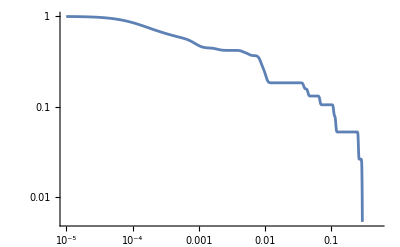

∫_0^∞ (∑_(i=1)^n (BesselK[1,b_j] BesselK[2,b_i √(1+(2 x)/Total[Array[b_#1&,n]])] (∏_(k=1)^n BesselK[1,b_k √(1+(2 (delta+x))/Total[Array[b_#1&,n]])]/(BesselK[1,b_k] √(1+(2 (delta+x))/Total[Array[b_#1&,n]]))) (1+(2 (delta+x))/Total[Array[b_#1&,n]]) (∑_(j=1)^n BesselK[2,b_j √(1+(2 (delta+x))/Total[Array[b_#1&,n]])]/(BesselK[1,b_j] (2 (delta+x)+Total[Array[b_#1&,n]]))-BesselK[2,b_i √(1+(2 (delta+x))/Total[Array[b_#1&,n]])]/(BesselK[1,b_i] (2 (delta+x)+Total[Array[b_#1&,n]]))))/(BesselK[1,b_i √(1+(2 (delta+x))/Total[Array[b_#1&,n]])] BesselK[1,b_j √(1+(2 (delta+x))/Total[Array[b_#1&,n]])] (2 x+Total[Array[b_#1&,n]])))ⅆx

```mathematica
K=38
(*bvec=RandomInteger[{1,100},K]*)
bvec={8704,7633,3485,3230,2007,1324,1141,311,306,295,265,259,256,241,169,137,56,28,26,24,23,18,12,11,7,6,4,4,3,3,2,2,2,2,1,1,1,1}

Btot=Sum[bvec[[i]],{i,K}]

unnplb[l_,b_,B_]:=Exp[-((b-B  l)^2)/(2 B  l)]

clbzero[l_,B_]:=1-Exp[-(B  l)/2]

Zvec=Table[NIntegrate[unnplb[ll,bvec[[i]],Btot],{ll,0,1}],{i,K}]

marginalclb[l_]:=Sum[(1/K)*NIntegrate[unnplb[ll,bvec[[i]],Btot],{ll,l,1}]/Zvec[[i]],{i,K}]


LogLogPlot[{marginalclb[x]},{x,0.00001,0.5}]
```